```mathematica
Clear[Tlist,unstableBranches,stableBranches,numofuSB,numofSB,λuSB,λSB,λIuSB,λISB,findNum,linearfun,ϵ,TvQoPT,TDr1,TDr2,FuSB,FSB,FISB,FIuSB]
ϵ=10^-3;
Tlist[T_,xmin_,xmax_,num_]:=Tlist[T,xmin,xmax,num]=Array[{T,#}&,num,{xmin,xmax}]; 
(*Discretize r_+(T) by giving {{T,r}}*)
(*输入温度函数，基于区间生成的r得到{T，r}列表*)
unstableBranches[T_,xmin_,xmax_,num_]:=unstableBranches[T,xmin,xmax,num]=DeleteCases[Split[Tlist[T,xmin,xmax,num],First[#1]≥First[#2]&],{{x_,y_}}]; (*Find unstable branch*)
(*输入变量后得到列表，之后进行分割，*)
stableBranches[T_,xmin_,xmax_,num_]:=stableBranches[T,xmin,xmax,num]=DeleteCases[Split[Tlist[T,xmin,xmax,num],First[#1]≤First[#2]&],{{x_,y_}}];(* Find stable branch*)
numofuSB[T_,xmin_,xmax_,num_]:=numofuSB[T,xmin,xmax,num]=Length[unstableBranches[T,xmin,xmax,num]]; (* Number of unstable branch*)
numofSB[T_,xmin_,xmax_,num_]:=numofSB[T,xmin,xmax,num]=Length[stableBranches[T,xmin,xmax,num]]; (* Number of stable branch*)
λuSB[Q_,L_,T_,xmin_,xmax_,num_]:=If[numofuSB[T,xmin,xmax,num]==0,{},MapAt[λ[#,Q,L]&,unstableBranches[T,xmin,xmax,num],{{All,All,2}}]]; 
(* λ of unstable branch*)
λSB[Q_,L_,T_,xmin_,xmax_,num_]:=λSB[Q,L,T,xmin,xmax,num]=If[numofSB[T,xmin,xmax,num]==0,{},MapAt[λ[#,Q,L]&,stableBranches[T,xmin,xmax,num],{{All,All,2}}]](* λ of stable branch*)
λIuSB[t_,i_,Q_,L_,T_,xmin_,xmax_,num_,order_]:=λIuSB[t,i,Q,L,T,xmin,xmax,num,order]=If[t≥Max[0,Min[λuSB[Q,L,T,xmin,xmax,num][[i,1,1]],λuSB[Q,L,T,xmin,xmax,num][[i,-1,1]]]]&&t≤Max[0,Max[λuSB[Q,L,T,xmin,xmax,num][[i,1,1]],λuSB[Q,L,T,xmin,xmax,num][[i,-1,1]]]],Interpolation[λuSB[Q,L,T,xmin,xmax,num][[i]],InterpolationOrder->order][t]];(*Interpolation λ of unstable branch*)
λISB[t_,i_,Q_,L_,T_,xmin_,xmax_,num_,order_]:=λISB[t,i,Q,L,T,xmin,xmax,num,order]=If[t≥Max[0,Min[λSB[Q,L,T,xmin,xmax,num][[i,1,1]],λSB[Q,L,T,xmin,xmax,num][[i,-1,1]]]]&&t≤Max[0,Max[λSB[Q,L,T,xmin,xmax,num][[i,1,1]],λSB[Q,L,T,xmin,xmax,num][[i,-1,1]]]],Interpolation[λSB[Q,L,T,xmin,xmax,num][[i]],InterpolationOrder->order][t]];(*Interpolation of λ of stable branch*)
FuSB[F_,T_,xmin_,xmax_,num_]:=FuSB[F,T,xmin,xmax,num]=If[numofuSB[T,xmin,xmax,num]==0,{},MapAt[F&,unstableBranches[T,xmin,xmax,num],{{All,All,2}}]]; (* Free energy of unstable branch*)
FSB[F_,T_,xmin_,xmax_,num_]:=FSB[F,T,xmin,xmax,num]=If[numofSB[T,xmin,xmax,num]==0,{},MapAt[F&,stableBranches[T,xmin,xmax,num],{{All,All,2}}]](* Free energy of stable branch*)
FIuSB[t_,i_,F_,T_,xmin_,xmax_,num_,order_]:=FIuSB[t,i,F,T,xmin,xmax,num,order]=If[t≥Max[0,Min[FuSB[F,T,xmin,xmax,num][[i,1,1]],FuSB[F,T,xmin,xmax,num][[i,-1,1]]]]&&t≤Max[0,Max[FuSB[F,T,xmin,xmax,num][[i,1,1]],FuSB[F,T,xmin,xmax,num][[i,-1,1]]]],Interpolation[FuSB[F,T,xmin,xmax,num][[i]],InterpolationOrder->order][t]];(*Interpolation of free energy of unstable branch*)
FISB[t_,i_,F_,T_,xmin_,xmax_,num_,order_]:=FISB[t,i,F,T,xmin,xmax,num,order]=If[t≥Max[0,Min[FSB[F,T,xmin,xmax,num][[i,1,1]],FSB[F,T,xmin,xmax,num][[i,-1,1]]]]&&t≤Max[0,Max[FSB[F,T,xmin,xmax,num][[i,1,1]],FSB[F,T,xmin,xmax,num][[i,-1,1]]]],Interpolation[FSB[F,T,xmin,xmax,num][[i]],InterpolationOrder->order][t]];(*Interpolation of free energy of stable branch*)
linearfun[x_,{x0_,y0_},{x1_,y1_}]:=(y1-y0)/(x1-x0)(x-x0)+y0;(*Define the linear interpolation function*)
findNum[list_,num_]:=findNum[list,num]=Block[{splist,l},splist=Split[list,(Last[#1]<num&&Last[#2]< num)||(Last[#1]>num&&Last[#2]>num)&];l=Length[splist];Union[Table[linearfun[num,Reverse[splist[[i,-1]]],Reverse[splist[[i+1,1]]]],{i,1,l-1}]]];(*Given y, find the corresponding x in the list of {{x,y}}*)
TvQoPT[F_,T_,xmin_,xmax_,num_,shift_,order_]:=FindRoot[FISB[t,1,F,T,xmin,xmax,num,order]==FISB[t,2,F,T,xmin,xmax,num,order],{t,Min[FSB[F,T,xmin,xmax,num][[2,1,1]],FSB[F,T,xmin,xmax,num][[2,-1,1]]]+shift}];
(*Find the phase transition temperature T for Q*)


TDr1[r_,Q_]:=D[T[r,Q],r]//Simplify;
TDr2[r_,Q_]:=D[T[r,Q],{r,2}]//Simplify;

Clear[T,En,F,Qr,Φ,M,U,rc,Qc,Tc,λ,fDr1,fDr2,L,rps,f,Tplist,Tp,Δλ]
T[r_,Q_]=1/(4π r)(1-Q^2/r^2+3 r^2);
(*Define the temeprature*)
En[r_,Q_]=(Q^2+r^2+r^4)/(2r);
(*Define the energy*)
F[r_,Q_]=En[r,Q]-T[r,Q] π r^2//Simplify;(*Define the free energy*)
Qr[r_,Q_]=Q;
(*Define the charge*)
Φ[r_,Q_]=Q/r;
(*Define the potential*)
M[r_,Q_]=r/2(1+Q^2/r^2+r^2);
(*Define the mass*)
U[r_,Q_]=M[r,Q]-Qr[r,Q]Φ[r,Q];
(*Define the internal energy*)

rps[r_,Q_,L_]:=rps[r,Q,L]=(*FindRoot[L^2*(x^2-3*M[r,Q]*x+2 Q^2)==M[r,Q]*x^3-Q^2*x^2+x^6,{x,r+0.1,r,100},WorkingPrecision->60][[1,2]]*)Block[{m},m=SelectFirst[Flatten@Values@NSolve[L^2*(x^2-3*M[r,Q]*x+2 Q^2)==M[r,Q]*x^3-Q^2*x^2+x^6,x,Reals],#>r&];m];

f[r_,Q_,L_] :=f[r,Q,L] =1- (2M[r,Q])/rps[r,Q,L]+Q^2/rps[r,Q,L]^2+rps[r,Q,L]^2;
fDr1[r_,Q_,L_]:=fDr1[r,Q,L]= (2M[r,Q])/rps[r,Q,L]^2-2*Q^2/rps[r,Q,L]^3+2*rps[r,Q,L];
fDr2[r_,Q_,L_]:=fDr2[r,Q,L]=(-4M[r,Q])/rps[r,Q,L]^3+6*Q^2/rps[r,Q,L]^4+2;
λ[r_,Q_,L_]:=λ[r,Q,L]=1/(√2)Sqrt[(-((3*f[r,Q,L]*fDr1[r,Q,L])/rps[r,Q,L]-2*fDr1[r,Q,L]^2+f[r,Q,L]*fDr2[r,Q,L]))];
(*Define f and its Dr*)
rc=FindRoot[{TDr1[r,Q]==0,TDr2[r,Q]==0},{{r,0.1},{Q,0.1}}][[1,2]];
Qc=FindRoot[{TDr1[r,Q]==0,TDr2[r,Q]==0},{{r,0.1},{Q,0.1}}][[2,2]];
Tc=T[rc,Qc];
{rc,Qc,Tc}
(*Critical values of r,Q and T*)
lineStyle={Black,Dotted};
lineStyleP={Black,Dashed};
λ[0.4552477245,0.2,3]
```

{0.408248,0.166667,0.259899}

0.00787509

```mathematica
|\
```

```mathematica
、
```

```mathematica
\
```

```mathematica
(*Plot λ and R with the respect T for Q<Subscript[Q, c]*)
q=0.08;xmin=0.0001;xmax=0.8782608235;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=20;qmin=0.09;qmax=Qc-0.005;qnum=30;
rru={t1=λSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],100};(*The upper point of the vertical line T=Subscript[T, 2]*)
rrd={λSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],down};(*The lower point of the vertical line T=Subscript[T, 2]*)
llu={t2=λuSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],100};
(*The upper point of the vertical line T=Subscript[T, 1]*)
lld={λuSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],down};
(*The lower point of the vertical line T=Subscript[T, 1]*)
tpu={tp=TvQoPT[F[#,q],T[#,q],xmin,xmax,num,0.001,2][[1,2]],100(*findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[1]]),tp][[1]]*)};
(*The upper point of the phase transition line T=Subscript[T, p]*)
tpd={tp,down};
(*The lower point of the phase transition line T=Subscript[T, p]*)
TvFSQ1=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.45},{Flower,3}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*),Epilog->{{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyle],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Text[Style[Subscript[T̃, p], FontSize ->8], {tp-0.005, 0.1}]},{Text[Style[Subscript[T̃, 1], FontSize ->8],{t1-0.005, 0.1}]},{Text[Style[Subscript[T̃, 2], FontSize ->8], {t2-0.005, 0.1}]}}](*Plot of λ versus T*)
TvFSQ=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.1,0.26},{Flower,1.5}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*)(*,Epilog->{{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyle],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Text[Style[Subscript[T, p], FontSize ->8], {tp-0.005, 0.1}]},{Text[Style[Subscript[T, 1], FontSize ->8],{t1-0.005, 0.1}]},{Text[Style[Subscript[T, 2], FontSize ->8], {t2-0.005, 0.1}]}}*)]
Tp[q_]:=TvQoPT[F[#,q],T[#,q],xmin,xmax,num,0.001,2][[1,2]];
Δλ[q_]:=(findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[1]]),Tp[q]][[1]])-(findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[-1]]),Tp[q]][[1]]);
Tplist[qmin_,qmax_,qnum_]:=Table[{Tp[i],Δλ[i]},{i,qmin,qmax,(qmax-qmin)/(qnum-1)}]; 

(*TvFSQ=ListLinePlot[Tplist[qmin,qmax,qnum],PlotRange->{{0.25,0.32},{0,2}},PlotStyle->{Blue},AxesLabel->{Subscript[T, p],Δλ},Epilog->{{Text[Style[Subscript[T, c], FontSize ->8], {Tc, 0.10}]}}]*)


(*denplot=Show[DensityPlot[λ[r,Q,3],{Q,0.001,0.5},{r,0.001,0.5},PlotLegends->Automatic,AxesLabel->{Q,r},ColorFunction->"TemperatureMap",PlotPoints->100],Plot[(√(-1+√(1+12 *x^2)))/(√6),{x,0.001,0.5},Filling->Axis,FillingStyle->LightGray]]*)
(*DensityPlot[λ[r,0.08,L],{L,0.1,30},{r,0.1,1},PlotLegends->Automatic,AxesLabel->{Q,r},ColorFunction->"TemperatureMap",PlotRange->All,PlotPoints->500]*)
(*Array[λ[#1,0.08,#2]&,{100,100},{{0.001,1},{0.001,30}}]*)
(*Plot3D[λ[r,0.08,L],{L,0,30},{r,0.1,1.0}]*)
(*Select[Flatten@Values@NSolve[20^2*(x^2-3*M[0.5,0.08]*x+2*0.08^2)==M[0.5,0.08]*x^3-0.08^2*x^2+x^6,x,Reals],#>0.5&][[-1]]*)
(*λ[0.1,0.08,5]
λ[0.1,0.08,30]
Select[Flatten@Values@NSolve[5^2*(x^2-3*M[0.1,0.08]*x+2*0.08^2)==M[0.1,0.08]*x^3-0.08^2*x^2+x^6,x,Reals],#>0.1&][[-1]]
NSolve[5^2*(x^2-3*M[0.1,0.08]*x+2*0.08^2)==M[0.1,0.08]*x^3-0.08^2*x^2+x^6,x,Reals]
NSolve[30^2*(x^2-3*M[0.1,0.08]*x+2*0.08^2)==M[0.1,0.08]*x^3-0.08^2*x^2+x^6,x,Reals]
rps[0.1,0.08,5]
rps[0.1,0.08,30]*)
```

```mathematica
q=0.2;xmin=0.0001;xmax=0.8782608235;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=20;qmin=0.09;qmax=Qc-0.005;qnum=30;
TvFSQ=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.32},{Flower,1.5}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ},Epilog->{{Directive[lineStyleP],Line[{{t1=T[xmax,0.2],-100},{t1,100}}]},{Text[Style[Subscript[T̃, t], FontSize ->8], {t1-0.003, 0.05}]}}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*)(*,Epilog->{{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyle],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Text[Style[Subscript[T, p], FontSize ->8], {tp-0.005, 0.1}]},{Text[Style[Subscript[T, 1], FontSize ->8],{t1-0.005, 0.1}]},{Text[Style[Subscript[T, 2], FontSize ->8], {t2-0.005, 0.1}]}}*)]
```

```mathematica
q=0.2;xmin=0.0001;xmax=0.4552477245;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=3;qmin=0.09;qmax=Qc-0.005;qnum=30;
TvFSQ=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.32},{Flower,1.5}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ},Epilog->{{Directive[lineStyleP],Line[{{t1=T[xmax,0.2],-100},{t1,100}}]},{Text[Style[Subscript[T̃, t], FontSize ->8], {t1-0.003, 0.05}]}}]
```

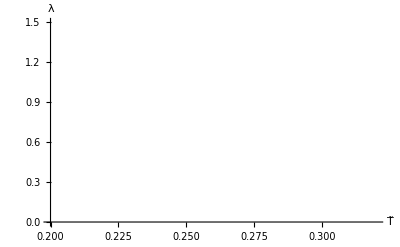

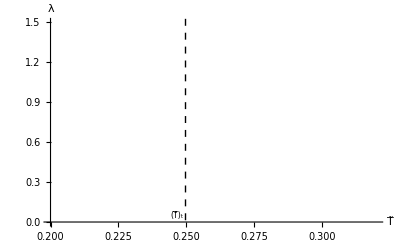

```mathematica
q=0.2;xmin=0.0001;xmax=0.4552477245;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=0.3;qmin=0.09;qmax=Qc-0.005;qnum=30;
TvFSQ=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.32},{Flower,1.5}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ}]
```

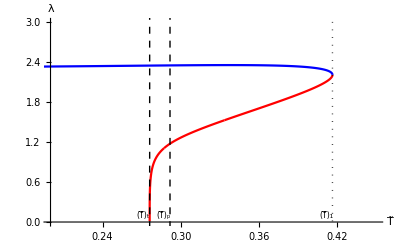

```mathematica
q=0.08;xmin=0.001;xmax=0.4756592765;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=3;qmin=0.09;qmax=Qc-0.005;qnum=30;
rru={t1=λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],100};(*The upper point of the vertical line T=Subscript[T, 2]*)
rrd={λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],down};(*The lower point of the vertical line T=Subscript[T, 2]*)
llu={t2=T[xmax,0.08],100};
(*The upper point of the vertical line T=Subscript[T, 1]*)
lld={t2,down};
(*The lower point of the vertical line T=Subscript[T, 1]*)
tpu={tp=TvQoPT[F[#,q],T[#,q],xmin,2,num,0.001,2][[1,2]],100(*findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[1]]),tp][[1]]*)};
(*The upper point of the phase transition line T=Subscript[T, p]*)
tpd={tp,down};
(*The lower point of the phase transition line T=Subscript[T, p]*)
TvFSQ1=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.45},{Flower,3}},PlotStyle->{Blue,Red},AxesLabel->{T̃,λ}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*),Epilog->{{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyleP],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Text[Style[Subscript[T̃, p], FontSize ->8], {tp-0.005, 0.1}]},{Text[Style[Subscript[T̃, 1], FontSize ->8],{t1-0.005, 0.1}]},{Text[Style[Subscript[T̃, t], FontSize ->8], {t2-0.005, 0.1}]}}](*Plot of λ versus T*)
```

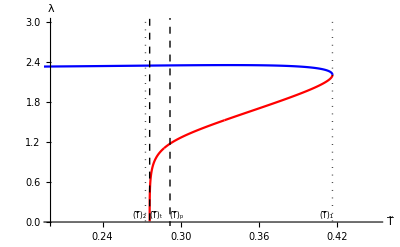

```mathematica
q=0.08;xmin=0.001;xmax=0.4756592765;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=3;qmin=0.09;qmax=Qc-0.005;qnum=30;
rru={t1=λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],100};(*The upper point of the vertical line T=Subscript[T, 2]*)
rrd={λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],down};(*The lower point of the vertical line T=Subscript[T, 2]*)
llu={t2=λuSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],100};
(*The upper point of the vertical line T=Subscript[T, 1]*)
lld={λuSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],down};
(*The lower point of the vertical line T=Subscript[T, 1]*)
tpu={tp=TvQoPT[F[#,q],T[#,q],xmin,2,num,0.001,2][[1,2]],100(*findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[1]]),tp][[1]]*)};
(*The upper point of the phase transition line T=Subscript[T, p]*)
tpd={tp,down};
(*The lower point of the phase transition line T=Subscript[T, p]*)
TvFSQ1=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.45},{Flower,3}},PlotStyle->{Blue,Red},AxesLabel->{T̃,λ}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*),Epilog->{{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyle],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Directive[lineStyleP],Line[{{tt=T[xmax,0.08],-100},{tt,100}}]},{Text[Style[Subscript[T̃, p], FontSize ->8], {tp+0.005, 0.1}]},{Text[Style[Subscript[T̃, 1], FontSize ->8],{t1-0.005, 0.1}]},{Text[Style["(T̃)_2", FontSize ->8], {t2-0.005, 0.1}]},{Text[Style[Subscript[T̃, t], FontSize ->8], {tt+0.005, 0.1}]}}](*Plot of λ versus T*)
```

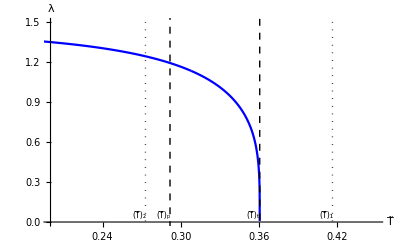

```mathematica
q=0.08;xmin=0.001;xmax=0.10850044325;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=0.3;qmin=0.09;qmax=Qc-0.005;qnum=30;
rru={t1=λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],100};(*The upper point of the vertical line T=Subscript[T, 2]*)
rrd={λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],down};(*The lower point of the vertical line T=Subscript[T, 2]*)
llu={t2=λuSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],100};
(*The upper point of the vertical line T=Subscript[T, 1]*)
lld={λuSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],down};
(*The lower point of the vertical line T=Subscript[T, 1]*)
tpu={tp=TvQoPT[F[#,q],T[#,q],xmin,2,num,0.001,2][[1,2]],100(*findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[1]]),tp][[1]]*)};
(*The upper point of the phase transition line T=Subscript[T, p]*)
tpd={tp,down};
(*The lower point of the phase transition line T=Subscript[T, p]*)
TvFSQ1=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.45},{Flower,1.5}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*),Epilog->{{Directive[lineStyleP],Line[{{tt=T[xmax,0.08],-100},{tt,100}}]},{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyle],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Text[Style[Subscript[T̃, p], FontSize ->8], {tp-0.005, 0.05}]},{Text[Style[Subscript[T̃, 1], FontSize ->8],{t1-0.005, 0.05}]},{Text[Style[Subscript[T̃, 2], FontSize ->8], {t2-0.005, 0.05}]},{Text[Style[Subscript[T̃, t], FontSize ->8], {tt-0.005, 0.05}]}}](*Plot of λ versus T*)
```

```mathematica
q=0.2;xmin=0.001;xmax=0.889728253;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=20;qmin=0.09;qmax=Qc-0.005;qnum=30;
rru={t1=λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],100};(*The upper point of the vertical line T=Subscript[T, 2]*)
rrd={λSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],down};(*The lower point of the vertical line T=Subscript[T, 2]*)
llu={t2=λuSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],100};
(*The upper point of the vertical line T=Subscript[T, 1]*)
lld={λuSB[q,L,T[#,q],xmin,2,num][[1,-1,1]],down};
(*The lower point of the vertical line T=Subscript[T, 1]*)
tpu={tp=TvQoPT[F[#,q],T[#,q],xmin,2,num,0.001,2][[1,2]],100(*findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[1]]),tp][[1]]*)};
(*The upper point of the phase transition line T=Subscript[T, p]*)
tpd={tp,down};
(*The lower point of the phase transition line T=Subscript[T, p]*)
TvFSQ=ListLinePlot[λSB[q,L,T[#,q],xmin,xmax,num],PlotRange->{{0,0.35},{Flower,1.5}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*),Epilog->{{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyle],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Text[Style[Subscript[T̃, p], FontSize ->8], {tp-0.005, 0.05}]},{Text[Style[Subscript[T̃, 1], FontSize ->8],{t1-0.005, 0.05}]},{Text[Style[Subscript[T̃, 2], FontSize ->8], {t2-0.005, 0.05}]}}](*Plot of λ versus T*)
```

$Aborted

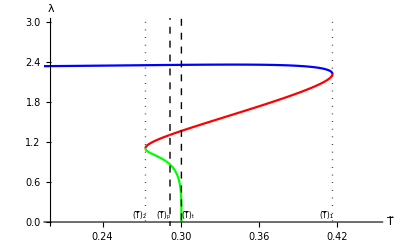

Part::partw: {{{-509216.,4.80025},{-485788.,4.72549},{-463775.,4.65302},{-443072.,4.58274},{-423583.,4.51456},{-405220.,4.44837},{-387904.,4.3841},{-371560.,4.32165},{-356121.,4.26096},«33»,{-110381.,2.88409},{-107292.,2.85694},{-104316.,2.8303},{-101450.,2.80415},{-98687.1,2.77847},{-96024.1,2.75327},{-93455.9,2.72852},{-90978.5,2.70421},«8927»}} 的部分 2 不存在.

FindRoot::srect: 搜索指定 {t,Min[FSB[0.0048 Power[«2»]+0.25 Slot[«1»]-0.25 Power[«2»],(1+Times[«2»]+Times[«2»])/(4 π Slot[«1»]),0.001,0.475659,30000]⟦2,1,1⟧,FSB[0.0048 Power[«2»]+0.25 Slot[«1»]-0.25 Power[«2»],(1+Times[«2»]+Times[«2»])/(4 π Slot[«1»]),0.001,0.475659,30000]⟦2,-1,1⟧]+0.001} 中的值 0.001+Min[{{{-509216.,4.80025},{-485788.,4.72549},{-463775.,4.65302},{-443072.,4.58274},{-423583.,4.51456},{-405220.,4.44837},{-387904.,4.3841},{-371560.,4.32165},{-356121.,4.26096},«33»,{-110381.,2.88409},{-107292.,2.85694},{-104316.,2.8303},{-101450.,2.80415},{-98687.1,2.77847},{-96024.1,2.75327},{-93455.9,2.72852},{-90978.5,2.70421},«8927»}}⟦2,-1,1⟧,«1»] 不是一个数，也不是由数字组成的数组.

-Graphics-

FindRoot::jsing: 在点 {r,Q} = {0.1,0.1} 碰到奇异雅克比. 尝试扰动初始点.

{0.1,0.1,0.310352}

$Aborted

$Aborted

```mathematica
q=0.08;xmin=0.0001;xmax=00.8852273;num=30000;Tupper=0.5;Flower=0;Fupper=9;down=-150;L=20;qmin=0.09;qmax=Qc-0.005;qnum=30;
rru={t1=λSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],100};(*The upper point of the vertical line T=Subscript[T, 2]*)
rrd={λSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],down};(*The lower point of the vertical line T=Subscript[T, 2]*)
llu={t2=λuSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],100};
(*The upper point of the vertical line T=Subscript[T, 1]*)
lld={λuSB[q,L,T[#,q],xmin,xmax,num][[1,-1,1]],down};
(*The lower point of the vertical line T=Subscript[T, 1]*)
tpu={tp=TvQoPT[F[#,q],T[#,q],xmin,xmax,num,0.001,2][[1,2]],100(*findNum[Reverse/@(λSB[q,L,T[#,q],xmin,xmax,num][[1]]),tp][[1]]*)};
(*The upper point of the phase transition line T=Subscript[T, p]*)
tpd={tp,down};
(*The lower point of the phase transition line T=Subscript[T, p]*)
TvFSQ1=ListLinePlot[Join[λSB[q,L,T[#,q],xmin,xmax,num],λuSB[q,L,T[#,q],xmin,xmax,num]],PlotRange->{{0.2,0.45},{Flower,3}},PlotStyle->{Blue,Green,Red},AxesLabel->{T̃,λ}(*,PlotLegends->Placed[{"Small BH","Large BH","Intermediate BH"},{0.80,0.25}]*),Epilog->{{Directive[lineStyleP],Line[{{t3=T[xmax,0.08],-100},{t3,1000}}]},,{Directive[lineStyle],Line[{rru,rrd}]},{Directive[lineStyle],Line[{llu,lld}]},{Directive[lineStyleP],Line[{tpu,tpd}]},{Text[Style[Subscript[T̃, p], FontSize ->8], {tp-0.005, 0.1}]},{Text[Style[Subscript[T̃, 1], FontSize ->8],{t1-0.005, 0.1}]},{Text[Style[Subscript[T̃, 2], FontSize ->8], {t2-0.005, 0.1}]},{Text[Style[Subscript[T̃, t], FontSize ->8], {t3+0.005, 0.1}]}}](*Plot of λ versus T*)
```

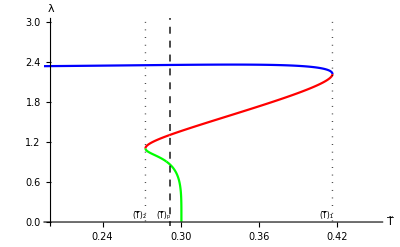

```mathematica
Show[TvFSQ1,ImageSize->Tiny]
```

```mathematica
λ[0.8782608235,0.2,20]
```

0.00786747

```mathematica
\
```

{0.408248,0.166667,0.259899}

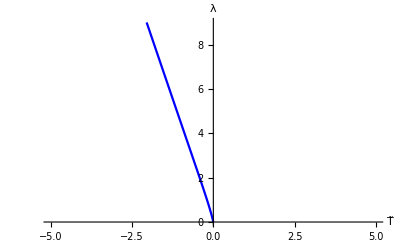

0.000983236

```mathematica
|
```

```mathematica
NumberForm[0.3201555842189555,16]
```

0.3201555842189555

```mathematica
2.1667232996860455
```

{{x→-2.29925},{x→0.0736102},{x→0.173997},{x→2.16672}}

{{x→-5.53865},{x→0.0736096},{x→0.173893},{x→5.41344}}

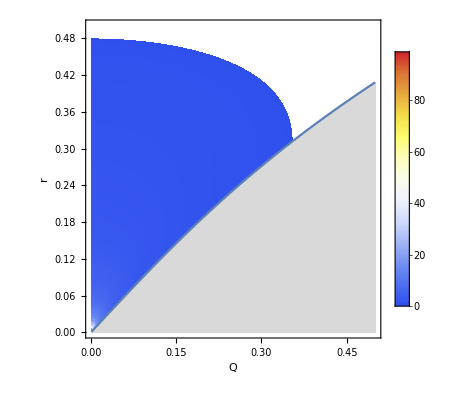
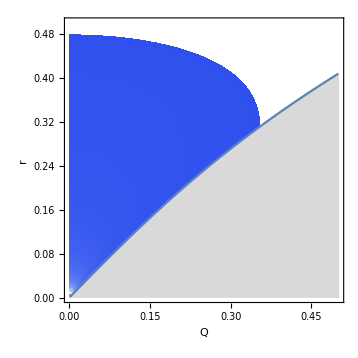

-Graphics3D-

```mathematica
{0.40824829046386285,0.1666666666666669,0.25989893374455864}
```

{0.408248,0.166667,0.259899}

FindRoot::nlnum: 在 {x} = {0.} 处，函数值 {0.+L^2 (0.+2. Q^2)} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot::nlnum 的进一步输出将被抑制.

FindRoot::nlnum: 在 {x} = {1.49012×10^-8} 处，函数值 {3.75255×10^-18-1.65436×10^-24 #1 (1+0.0169/#1^2+#1^2)+100 (0.0338-2.23517×10^-8 #1 (1+0.0169 Power[«2»]+Slot[«1»]^2))} 不是由数字组成的维度为 {1} 的列表.

FindRoot::srect: 搜索指定 {x,r} 中的值 r 不是一个数，也不是由数字组成的数组.

General::stop: 在本次计算中，FindRoot::srect 的进一步输出将被抑制.

FindRoot::srect: 搜索指定 {x,r} 中的值 r 不是一个数，也不是由数字组成的数组.

General::stop: 在本次计算中，FindRoot::srect 的进一步输出将被抑制.

FindRoot::srect: 搜索指定 {x,r} 中的值 r 不是一个数，也不是由数字组成的数组.

General::stop: 在本次计算中，FindRoot::srect 的进一步输出将被抑制.

FindRoot::srect: 搜索指定 {x,r} 中的值 r 不是一个数，也不是由数字组成的数组.

General::stop: 在本次计算中，FindRoot::srect 的进一步输出将被抑制.

FindRoot::srect: 搜索指定 {x,r} 中的值 r 不是一个数，也不是由数字组成的数组.